```mathematica
ClearAll["Global`*"]
x[t_] := r1*-Sin[a1[t]]
y[t_] := r1*Cos[a1[t]]
```

```mathematica
T = Simplify[TrigReduce[1/2*m(x'[t]^2+y'[t]^2)]]
```

1/2 m r1^2 a1'[t]^2

```mathematica
(*k = {k1, k2, k3, k4};(*, 100, 100};*)
ra = {ra1, ra2};(*,.02};*)
Lang = {{d11, d12},{d21, d22},{-d31,d32}, {d41,-d42}};
initDef = {def1, def2, def3, def4};*)
k = {k1, k2};
ra = {ra1};
friction = {fr1};
Lang={{d11},{d21}};
initDef = {def1, def2};
(*,{-1,1}, {1,-1}};*)(*-1 means clockwise, 1 means counter clockwise*)
```

```mathematica
V = 1/2*(k[[1]]*(Lang[[1,1]]*a1[t]*ra[[1]]+initDef[[1]])^2+
k[[2]]*(Lang[[2,1]]*a1[t]*ra[[1]]+initDef[[2]])^2)
```

1/2 (k1 (def1+d11 ra1 a1[t])^2+k2 (def2+d21 ra1 a1[t])^2)

```mathematica
(*WITHOUT THIS FRICTION THE OBJECT OSCILLATES CONSTANTLY*)
Fr = 1/2*friction[[1]]*a1'[t]^2
```

1/2 fr1 a1'[t]^2

```mathematica
L = T-V
H= T+V
```

1/2 (-k1 (def1+d11 ra1 a1[t])^2-k2 (def2+d21 ra1 a1[t])^2)+1/2 m r1^2 a1'[t]^2

1/2 (k1 (def1+d11 ra1 a1[t])^2+k2 (def2+d21 ra1 a1[t])^2)+1/2 m r1^2 a1'[t]^2

```mathematica
a1Solve = Simplify[D[D[L,a1'[t]],t]==D[L,a1[t]] - D[Fr,a1'[t]]]
```

d11 def1 k1 ra1+d21 def2 k2 ra1+(d11^2 k1+d21^2 k2) ra1^2 a1[t]+fr1 a1'[t]+m r1^2 a1''[t]==0

```mathematica
sol = Simplify[TrigReduce[Solve[a1Solve, a1''[t]]]][[1]]
(*a2sol = Simplify[TrigReduce[Solve[a2Solve, a2''[t]][[1]]]]*)
```

{a1''[t]→-(d11 def1 k1 ra1+d21 def2 k2 ra1+(d11^2 k1+d21^2 k2) ra1^2 a1[t]+fr1 a1'[t])/(m r1^2)}

```mathematica
(*THIS SYSTEM ASSUMES MASS IS AT TIP OF FINGER OBJECT*)
```

```mathematica
parameters = {
m->1,

r1->1/20,

k1->100,
k2->100,

ra1->1/50,

fr1->.02,

d11->-1,
d21->1,

def1->1/20,
def2->1/20
};
soltime = 5;
```

```mathematica
governingEq1 = Simplify[TrigReduce[a1''[t]==(a1''[t]/.sol)/.parameters]]//FullSimplify
```

a1''[t]==-32. a1[t]-8. a1'[t]

```mathematica
s = NDSolve[{governingEq1,a1[0]==1, a1'[0]== 0},a1[t],{t,0,soltime}][[1]]//FullSimplify;
finsol = {s[[1]],D[s,t][[1]], D[s,{t,2}][[1]]}
```

{a1[t]→InterpolatingFunction[{{0., 5.}}, <>][t],a1'[t]→InterpolatingFunction[{{0., 5.}}, <>][t],a1''[t]→InterpolatingFunction[{{0., 5.}}, <>][t]}

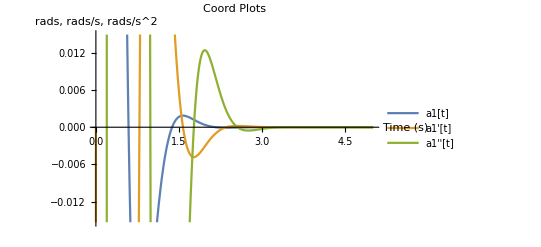

```mathematica
Plot[{a1[t]/.finsol, a1'[t]/.finsol, a1''[t]/.finsol},{t,0,soltime},PlotLabel->"Coord Plots", PlotLegends->{"a1[t]", "a1'[t]", "a1''[t]"},AxesLabel->{"Time (s)","rads, rads/s, rads/s^2"}, PlotRange->Automatic]
```

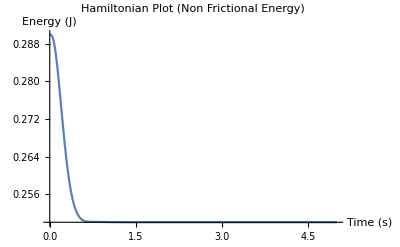

```mathematica
Plot[Evaluate[H/.parameters/.finsol],{t,0,soltime},PlotLabel->"Hamiltonian Plot (Non Frictional Energy)",AxesLabel->{"Time (s)","Energy (J)"},PlotRange->Full]
```

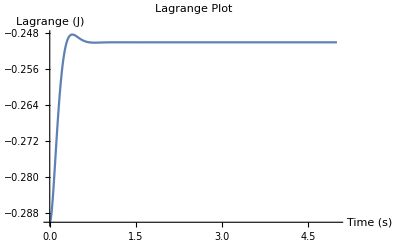

```mathematica
Plot[Evaluate[L/.parameters/.finsol],{t,0,soltime},PlotLabel->"Lagrange Plot",AxesLabel->{"Time (s)","Lagrange (J)"}, PlotRange->Full]
```

```mathematica
Evaluate[{x[t],y[t]}/.parameters/.s[[1]]]
```

{-1/20 Sin[InterpolatingFunction[{{0., 5.}}, <>][t]],1/20 Cos[InterpolatingFunction[{{0., 5.}}, <>][t]]}

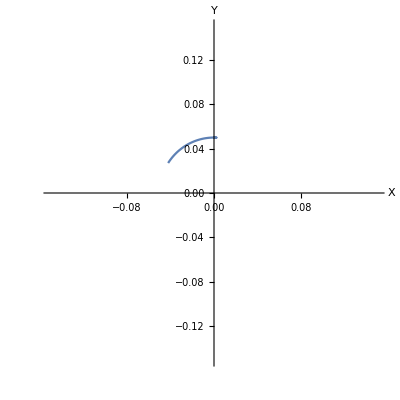

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s[[1]]],{t,0,soltime},PlotRange->{{-.15,.15},{-.15,.15}},AxesLabel-> {"X","Y"}]
```

```mathematica
tailLen = .2;
Animate[Show[{
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s[[1]]],{t,0,t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Orange},AxesLabel-> {"X","Y"}],
ParametricPlot[Evaluate[{x[t],y[t]}/.parameters/.s[[1]]],{t,Max[t0-tailLen,0],t0},AxesOrigin->{0,0},PlotRange->{{-.1,.1},{-.1, .1}},AspectRatio->1,ImageSize->500, PlotStyle->{Red,Thick},AxesLabel-> {"X","Y"}]

}],{t0, 0 ,soltime}]
```